# III.B Optical cavity

Lecamwasam, R, Iakovleva, T, & Twamley, J (2024). Quantum metrology with linear Lie algebra parameterizations Phys. Rev. Res., 6, 043137 arxiv:2311.12446.

See section III.B of the main text, and section III of the supplementary material.

Run OperatorAlgebrav2.nb before running this notebook.

## Lie algebra

```mathematica
Commutator[â,d̂,1];

algebra={1,â,d̂,d̂∘â};
```

### Commutation table

```mathematica
AlgCommTable[algebra]
```

| 1 | â | d̂ | d̂∘â
1 | 0 | 0 | 0 | 0
â | 0 | 0 | 1 | â
d̂ | 0 | -1 | 0 | -d̂
d̂∘â | 0 | -â | d̂ | 0

```mathematica
AlgCommTable[algebra,Xj->True]
```

| X_1 | X_2 | X_3 | X_4
X_1 | 0 | 0 | 0 | 0
X_2 | 0 | 0 | X_1 | X_2
X_3 | 0 | -X_1 | 0 | -X_3
X_4 | 0 | -X_2 | X_3 | 0

```mathematica
adjRep=AdjointRep[algebra];
Print["Adjoint representation:"]
Print[Subscript[ad, #[[1]]]," = ",MatrixForm@#[[2]]]&/@Transpose@{algebra,adjRep};
```

Adjoint representation:

ad_1 = (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

ad_(â) = (0 | 0 | 1 | 0
0 | 0 | 0 | 1
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

ad_(d̂) = (0 | -1 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | 0 | 0)

ad_(d̂∘â) = (0 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 0)

## Fernández solution

```mathematica
$Assumptions={0<θ<2π};
hCoeffs={0,-ⅈ η,ⅈ η,Δ};

Print["Hamilton: ",Ham=Total@Flatten@Thread@{hCoeffs*algebra}];
```

Hamilton: Δ d̂∘â-ⅈ η â+ⅈ η d̂

```mathematica
MakeLieH[hCoeffs,algebra,algebra]//FullSimplify//MatrixForm
```

(0 | 0 | 0 | 0
-ⅈ η | -Δ | 0 | 0
-ⅈ η | 0 | Δ | 0
0 | -ⅈ η | -ⅈ η | 0)

```mathematica
{ut,eom}=MakeLieEOM[hCoeffs,algebra,algebra]//FullSimplify;
sol=Flatten@DSolve[Flatten@eom,Flatten@ut,t]//FullSimplify
```

{u[1,1,t]→1,u[2,1,t]→(η (ⅈ (-1+Cos[t Δ])+Sin[t Δ]))/Δ,u[3,1,t]→-(ⅈ (-1+ⅇ^(ⅈ t Δ)) η)/Δ,u[4,1,t]→-(2 η^2 (-1+Cos[t Δ]))/Δ^2,u[1,2,t]→0,u[2,2,t]→ⅇ^(-ⅈ t Δ),u[3,2,t]→0,u[4,2,t]→(η (ⅈ (-1+Cos[t Δ])+Sin[t Δ]))/Δ,u[1,3,t]→0,u[2,3,t]→0,u[3,3,t]→ⅇ^(ⅈ t Δ),u[4,3,t]→-(ⅈ (-1+ⅇ^(ⅈ t Δ)) η)/Δ,u[1,4,t]→0,u[2,4,t]→0,u[3,4,t]→0,u[4,4,t]→1}

```mathematica
Table[u[j,k,t],{j,1,Length@algebra},{k,1,Length@algebra}]/.sol//TrigToExp//Simplify//MatrixForm
```

(1 | 0 | 0 | 0
-(ⅈ (1-ⅇ^(-ⅈ t Δ)) η)/Δ | ⅇ^(-ⅈ t Δ) | 0 | 0
-(ⅈ (-1+ⅇ^(ⅈ t Δ)) η)/Δ | 0 | ⅇ^(ⅈ t Δ) | 0
-(ⅇ^(-ⅈ t Δ) (-1+ⅇ^(ⅈ t Δ))^2 η^2)/Δ^2 | -(ⅈ (1-ⅇ^(-ⅈ t Δ)) η)/Δ | -(ⅈ (-1+ⅇ^(ⅈ t Δ)) η)/Δ | 1)

```mathematica
adt=Table[Sum[u[j,k,t]algebra[[k]],{k,1,Length@algebra}],{j,1,Length@algebra}]/.sol;
PrintSol[params_]:=(
Print["H = ",Ham/.params];
(Print[#[[1]],"(t) = ",#[[2]]]&/@Thread[{algebra,adt/.params//FullSimplify}];)
);

PrintSol[{}]
```

H = Δ d̂∘â-ⅈ η â+ⅈ η d̂

1(t) = 1

â(t) = ⅇ^(-ⅈ t Δ) â+(η (ⅈ (-1+Cos[t Δ])+Sin[t Δ]))/Δ

d̂(t) = (ⅈ η+ⅇ^(ⅈ t Δ) (-ⅈ η+Δ d̂))/Δ

d̂∘â(t) = d̂∘â+(-η (-1+Cos[t Δ]) (2 η-ⅈ Δ (â-d̂))+Δ η (â+d̂) Sin[t Δ])/Δ^2

```mathematica
PrintSol[{η->0}]
```

H = Δ d̂∘â

1(t) = 1

â(t) = ⅇ^(-ⅈ t Δ) â

d̂(t) = ⅇ^(ⅈ t Δ) d̂

d̂∘â(t) = d̂∘â

## Quantum Fisher information

### Solution using time-independent formula

```mathematica
hCoeffs={0,-ⅈ η,ⅈ η,θ};
(exparg=-ⅈ s Sum[hCoeffs[[j]]adjRep[[j]],{j,1,Length@algebra}])//MatrixForm
```

(0 | -s η | -s η | 0
0 | ⅈ s θ | 0 | -s η
0 | 0 | -ⅈ s θ | -s η
0 | 0 | 0 | 0)

```mathematica
(integrand=MatrixExp[exparg]//FullSimplify)//MatrixForm
```

(1 | (ⅈ (-1+ⅇ^(ⅈ s θ)) η)/θ | (ⅈ (1-ⅇ^(-ⅈ s θ)) η)/θ | -(2 η^2 (-1+Cos[s θ]))/θ^2
0 | ⅇ^(ⅈ s θ) | 0 | (ⅈ (-1+ⅇ^(ⅈ s θ)) η)/θ
0 | 0 | ⅇ^(-ⅈ s θ) | (ⅈ (1-ⅇ^(-ⅈ s θ)) η)/θ
0 | 0 | 0 | 1)

```mathematica
(eInt=Integrate[integrand,{s,0,t}]//FullSimplify)//MatrixForm
```

(t | (η (-1+ⅇ^(ⅈ t θ)-ⅈ t θ))/θ^2 | (η (-1+ⅇ^(-ⅈ t θ)+ⅈ t θ))/θ^2 | (2 η^2 (t θ-Sin[t θ]))/θ^3
0 | -(ⅈ (-1+ⅇ^(ⅈ t θ)))/θ | 0 | (η (-1+ⅇ^(ⅈ t θ)-ⅈ t θ))/θ^2
0 | 0 | (ⅈ (-1+ⅇ^(-ⅈ t θ)))/θ | (η (-1+ⅇ^(-ⅈ t θ)+ⅈ t θ))/θ^2
0 | 0 | 0 | t)

```mathematica
𝒱=Sum[D[hCoeffs[[j]],θ]eInt.Table[KroneckerDelta[k,j],{k,1,Length@algebra}],{j,1,Length@algebra}]//FullSimplify;
Print["𝒱 = ",Sum[𝒱[[j]]algebra[[j]],{j,1,Length@algebra}]]
```

𝒱 = t d̂∘â+(η (-1+ⅇ^(ⅈ t θ)-ⅈ t θ) â)/θ^2+(η (-1+ⅇ^(-ⅈ t θ)+ⅈ t θ) d̂)/θ^2+(2 η^2 (t θ-Sin[t θ]))/θ^3

```mathematica
Series[𝒱,{θ,0,0}]//Normal
```

{(t^3 η^2)/3,-(t^2 η)/2,-(t^2 η)/2,t}

### Solution using time-dependent formula

```mathematica
θVal=0;
dhj=D[hCoeffs,θ]
hj=hCoeffs
```

{0,0,0,1}

{0,-ⅈ η,ⅈ η,θ}

```mathematica
dvList=Table[(dhj[[j]]+ⅈ Sum[AlgStructureΓ[k,l,j,algebra]v[k,t]hj[[l]],{k,1,Length@algebra},{l,1,Length@algebra}]),{j,1,Length@algebra}]//FullSimplify;
vEqs=Table[D[v[j,t],t]==dvList[[j]],{j,1,Length@algebra}];
Print/@vEqs;
```

v^(0,1)[1,t]==-η (v[2,t]+v[3,t])

v^(0,1)[2,t]==ⅈ θ v[2,t]-η v[4,t]

v^(0,1)[3,t]==-ⅈ θ v[3,t]-η v[4,t]

v^(0,1)[4,t]==1

```mathematica
vIC=Table[v[j,0]==0,{j,1,Length@algebra}]
```

{v[1,0]==0,v[2,0]==0,v[3,0]==0,v[4,0]==0}

```mathematica
sol=Flatten@DSolve[Join[vEqs,vIC],Table[v[j,t],{j,1,Length@algebra}],t]//FullSimplify
```

{v[1,t]→(2 η^2 (t θ-Sin[t θ]))/θ^3,v[2,t]→(η (-1+ⅇ^(ⅈ t θ)-ⅈ t θ))/θ^2,v[3,t]→(η (-1+ⅇ^(-ⅈ t θ)+ⅈ t θ))/θ^2,v[4,t]→t}

## Wei Norman solution

```mathematica
permutations={{1,2,3,4},{1,2,4,3},{1,3,4,2}};
algebraList=Table[Permute[algebra,perm],{perm,permutations}]
weiCoeffsList=Table[Table[a[j,t]->-ⅈ Permute[hCoeffs,perm][[j]],{j,1,Length@algebra}],{perm,permutations}]
```

{{1,â,d̂,d̂∘â},{1,â,d̂∘â,d̂},{1,d̂∘â,â,d̂}}

{{a[1,t]→0,a[2,t]→-η,a[3,t]→η,a[4,t]→-ⅈ θ},{a[1,t]→0,a[2,t]→-η,a[3,t]→-ⅈ θ,a[4,t]→η},{a[1,t]→0,a[2,t]→-ⅈ θ,a[3,t]→-η,a[4,t]→η}}

```mathematica
vars=Table[u[j,t],{j,1,Length@algebra}];
wnIC=Table[u[j,0]==0,{j,1,Length@algebra}];
wnEOMList=Table[Join[WeiNormanEOM[algebraList[[j]]]/.weiCoeffsList[[j]],wnIC],{j,1,Length@permutations}];
```

```mathematica
paramsθ={η->5,θ->0.1};

j=3;

tf=10;
solj=Flatten@NDSolve[wnEOMList[[j]]/.paramsθ,vars,{t,0,tf}]
```

{u[1,t]→InterpolatingFunction[…][t],u[2,t]→InterpolatingFunction[…][t],u[3,t]→InterpolatingFunction[…][t],u[4,t]→InterpolatingFunction[…][t]}

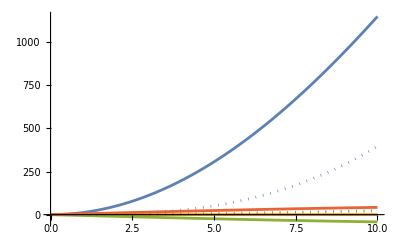

```mathematica
ReImPlot[vars/.solj//Evaluate,{t,0,tf},PlotRange->All]
```